# MyFunction

One-line description explaining the function’s basic purpose

## Definition

```mathematica
PositiveIntegerQ//ClearAll
```

```mathematica
PositiveIntegerQ[n_]:=And@@{IntegerQ[n],TrueQ[n∈PositiveIntegers]}
```

```mathematica
PositiveIntegerQ::usage="PositiveIntegerQ[n] returns True when n is a strictly positive integer.";
```

```mathematica
ClearAll[FindRandomHexagonalGridMazeSolution]
```

```mathematica
FindRandomHexagonalGridMazeSolution::usage="FindRandomHexagonalGridMazeSolution[{StyleBox[\"m\", \"TI\"],StyleBox[\"n\", \"TI\"]}] finds a solution and other data for a random hexagonal grid maze of size StyleBox[\"m\", \"TI\"] by StyleBox[\"n\", \"TI\"].";
```

```mathematica
FindRandomHexagonalGridMazeSolution[{m1_?PositiveIntegerQ /;!(m1<=1)(*equivalent to n>1. The reason I impose this constraint is the graph needs to be big enough to take away edges and still have edges. GridGraph[{1,1}] has no edges. This is known as the trivial graph, the singleton, or the unit graph.*),n1_?PositiveIntegerQ/;!(n1<=1)(*equivalent to n>1*)}]:=Module[{start,end,g,maze,m,solvedmaze,shortestPath,shortestPathSubgraph},g=ResourceFunction["HexagonalGridGraph"][{m1,n1}];m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]];maze=m;
start=1(*First@VertexList[m]*);end=m1*n1(*Last@VertexList[m]*) (*We are only removing edges, not vertices. The last vertex will always be the product of m and n.*);solvedmaze=HighlightGraph[m,PathGraph@(shortestPath=FindShortestPath[m,start,end])];shortestPathSubgraph=Subgraph[maze,shortestPath];<|"start"->start,"end"->end,"maze"->maze,"solved-maze"->solvedmaze,"shortest-path"->Iconize[shortestPath,"shortest-path"],"distance"->GraphDistance[m,start,end],"shortest-path-subgraph"->shortestPathSubgraph|>](*some ideas for other properties to add include deadends.*)
```

## Documentation

### Usage

MyFunction[arg]

explanation of what use of the argument arg does.

### Details & Options

Additional information about usage and options.

## Examples

### Basic Examples

Text about the example:

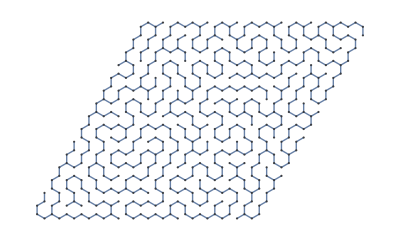
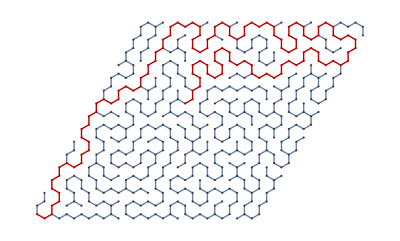
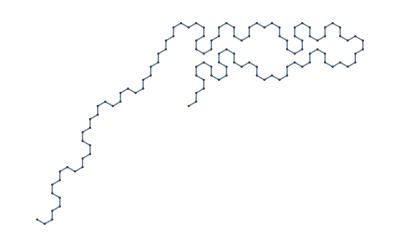
<|start→1,end→225,maze→-Graphics-,solved-maze→-Graphics-,shortest-path→,distance→119,shortest-path-subgraph→-Graphics-|>

```mathematica
FindRandomHexagonalGridMazeSolution[{15,15}]
```

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

### Applications

### Properties and Relations

### Possible Issues

### Neat Examples

## Source & Additional Information

### Contributed By

Author Name

### Keywords

keyword 1

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

SymbolName (documented Wolfram Language symbol)

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.